## 数据

```mathematica
raw="色泽 根蒂 敲声 纹理 脐部 触感 好瓜
青绿 蜷缩 浊响 清晰 凹陷 硬滑 是
乌黑 蜷缩 沉闷 清晰 凹陷 硬滑 是
乌黑 蜷缩 浊响 清晰 凹陷 硬滑 是
青绿 蜷缩 沉闷 清晰 凹陷 硬滑 是
浅白 蜷缩 浊响 清晰 凹陷 硬滑 是
青绿 稍蜷 浊响 清晰 稍凹 软粘 是
乌黑 稍蜷 浊响 稍糊 稍凹 软粘 是
乌黑 稍蜷 浊响 清晰 稍凹 硬滑 是
乌黑 稍蜷 沉闷 稍糊 稍凹 硬滑 否
青绿 硬挺 清脆 清晰 平坦 软粘 否
浅白 硬挺 清脆 模糊 平坦 硬滑 否
浅白 蜷缩 浊响 模糊 平坦 软粘 否
青绿 稍蜷 浊响 稍糊 凹陷 硬滑 否
浅白 稍蜷 沉闷 稍糊 凹陷 硬滑 否
乌黑 稍蜷 浊响 清晰 稍凹 软粘 否
浅白 蜷缩 浊响 模糊 平坦 硬滑 否
青绿 蜷缩 沉闷 稍糊 稍凹 硬滑 否";
raw2="色泽 根蒂 敲声 纹理 脐部 触感 好瓜
青绿 蜷缩 浊响 清晰 凹陷 硬滑 是
乌黑 蜷缩 沉闷 清晰 凹陷 硬滑 是
乌黑 蜷缩 浊响 清晰 凹陷 硬滑 是
青绿 蜷缩 沉闷 清晰 凹陷 硬滑 是
浅白 蜷缩 浊响 清晰 凹陷 硬滑 是
青绿 稍蜷 浊响 清晰 稍凹 软粘 是
乌黑 稍蜷 浊响 稍糊 稍凹 软粘 是
乌黑 稍蜷 浊响 清晰 稍凹 硬滑 是
乌黑 稍蜷 沉闷 稍糊 稍凹 硬滑 否
青绿 硬挺 清脆 清晰 平坦 软粘 否
浅白 硬挺 清脆 模糊 平坦 硬滑 否
浅白 蜷缩 浊响 模糊 平坦 软粘 否
青绿 稍蜷 浊响 稍糊 凹陷 硬滑 否
浅白 稍蜷 沉闷 稍糊 凹陷 硬滑 否
乌黑 稍蜷 浊响 清晰 稍凹 软粘 否
浅白 蜷缩 浊响 模糊 平坦 硬滑 否
青绿 蜷缩 沉闷 稍糊 稍凹 硬滑 否";
data=StringSplit[#," "]&/@StringSplit[raw2,"\n"];
properties=data[[1]];
trainingset=Rest[data];
```

## Tree Generation & Visualization

下面是一个通用的决策树生成及可视化函数。

SelectProperty：划分选择算法

Pre-pruning：是否进行预剪枝

Post-pruning：是否进行后剪枝

VerificationSet：剪枝时的验证集

```mathematica
CommonestDecision[l_]:=First@Commonest[l,1];
Attributes[SelectProperty]={ReadProtected};
Options[TreeGenerate]={SelectProperty->(1&),Prepruning->False,Postpruning->False,VerificationSet->{}};
TreeGenerate[training_,{},OptionsPattern[]]:=CommonestDecision@training[[All,-1]];TreeGenerate[training_,properties_,opts:OptionsPattern[]]:=Module[
{select=OptionValue[SelectProperty],propindex,c,s,prog,
final=CommonestDecision@training[[All,-1]],
post=OptionValue[Postpruning],veri=OptionValue[VerificationSet],correct1,correct2,newveri,r},
(*极端情况检查*)
c=Union@training[[All,-1]];
If[Length@c===1,Return@final];(*only one option now*)
If[SameQ@@Drop[training,None,{-1}],Return@final];

(*划分*)
propindex=select[training,properties];
s=SplitBy[SortBy[training,#[[propindex]]&],#[[propindex]]&];

correct1=Count[veri[[All,-1]],final];
If[OptionValue[Prepruning],
correct2=Total[With[{verdict=CommonestDecision@#[[All,-1]],key=#[[1,propindex]]},
Count[Select[veri,#[[propindex]]===key&][[All,-1]],verdict]]&/@s];
If[correct1≥correct2,Return@final]
];

prog=With[{key=#[[1,propindex]]},
newveri=Drop[Select[veri,#[[propindex]]===key&],None,{propindex}];
key->TreeGenerate[Drop[#,None,{propindex}],
Delete[properties,propindex],
VerificationSet->newveri,
opts]]&/@s;
r={propindex,prog};

If[OptionValue[Postpruning],
correct2=Count[BatchTestTree[r,veri],True];
If[correct1≥correct2,Return@final]
];
r
];
```

```mathematica
ClearAll[ApplyTree];
ApplyTree[v_?AtomQ,_]:=v;
ApplyTree[{node_,leafs_List},data_]/;Length[data]≥node:=With[{x=data[[node]]/.leafs},If[x=!=data[[node]],ApplyTree[x,Delete[data,node]],Indeterminate]];
ApplyTree[_,_]:=Indeterminate;
TestTree[tree_,case_]:=ApplyTree[tree,Most@case]===Last@case;
BatchTestTree[tree_,cases_]:=TestTree[tree,#]&/@cases;
```

```mathematica
Clear[DecisionTreeGraph];
DecisionTreeGraph[x_,properties_]:=Module[
{t,v,l},
t=DecisionTreeGraph[x,properties,{}];
v=Union@Flatten[t,2,DirectedEdge];
TreeGraph[t,VertexLabels->(#->Placed[Last@#,Center]&/@v),VertexSize->0.5, EdgeLabels->(#->#[[2,-2]]&/@t),VertexShapeFunction->(#->If[Cases[t,DirectedEdge[#,_]]==={},"Circle","Square"]&/@v)]
];
DecisionTreeGraph[{node_,leafs_List},properties_,prefix_]:=Module[
{next=Delete[properties,node],subs,this,all},
subs=DecisionTreeGraph[#[[2]],next,Append[prefix,#[[1]]]]&/@leafs;
this=Map[With[{t=If[Head@#1[[1]]=!=DirectedEdge,#1[[1]],#1[[1,1]]],n=Append[prefix,properties[[node]]]},n->t]&,subs];
all=Prepend[subs,this];
Cases[Flatten[all,1],_DirectedEdge]
];
DecisionTreeGraph[v_?AtomQ,_,prefix_]:={Append[prefix,v]};
```

```mathematica
tree=TreeGenerate[trainingset,Most@properties];
```

```mathematica
DecisionTreeGraph[tree,Most@properties]
```

## 划分选择

### ID3

以信息增益为准则选择划分属性。

```mathematica
SelectID3[dataset_,_]:=Last@SortBy[Range[1,Length[dataset[[1]]]-1],
InfoGain[Transpose@{dataset[[All,#]],dataset[[All,-1]]}]&];
InfoGain[dataset_]:=Module[
{groups},
groups=SplitBy[Sort[dataset],First];
-N@Total[Entropy[2,#[[All,-1]]]Length[#]/Length[dataset]&/@groups]
]
```

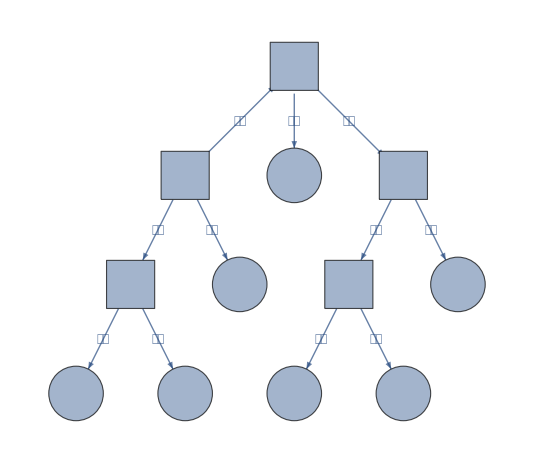

```mathematica
tree=TreeGenerate[trainingset[[{1,2,3,6,7,10,14,15,16,17}]],properties,SelectProperty->SelectID3];
DecisionTreeGraph[tree,properties]
```

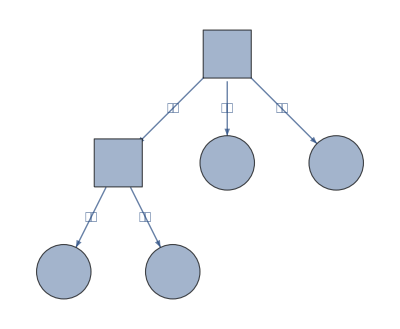

```mathematica
tree=TreeGenerate[trainingset[[{1,2,3,6,7,10,14,15,16,17}]],properties,SelectProperty->SelectID3,Postpruning->True,VerificationSet->trainingset[[{4,5,8,9,11,12,13}]]];
DecisionTreeGraph[tree,properties]
```

```mathematica
Count[{"是","是","是","否","否","否","否"},{"是"}]
```

0

```mathematica
tree
```

{是}

```mathematica
BatchTestTree@@{{4,{"清晰"->"是","稍糊"->"否"}},{{"青绿","蜷缩","沉闷","清晰","硬滑","是"},{"浅白","蜷缩","浊响","清晰","硬滑","是"},{"青绿","稍蜷","浊响","稍糊","硬滑","否"}}}
```

{True,True,True}

```mathematica
BatchTestTree[{5,{"凹陷"->"是","平坦"->"否","稍凹"->"否"}},trainingset[[{4,5,8,9,11,12,13}]]]
```

{True,True,False,True,True,True,False}

### C45

在ID3基础上引入固有值（即属性本身的熵）修正。

```mathematica
SelectC45[dataset_,_]:=Last@SortBy[Range[1,Length[dataset[[1]]]-1],
InfoGainRatio[Transpose@{dataset[[All,#]],dataset[[All,-1]]}]&];
InfoGainRatio[dataset_]:=Module[
{groups},
groups=SplitBy[Sort[dataset],First];
If[Length@groups>1,
-N@Total[Entropy[2,#[[All,-1]]]Length[#]/Length[dataset]&/@groups]/Entropy[2,dataset[[All,1]]],
-∞]
]
```

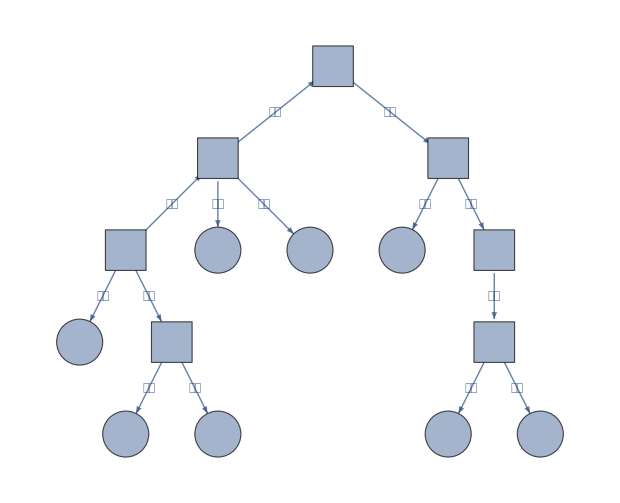

```mathematica
tree=TreeGenerate[trainingset,properties,SelectProperty->SelectC45];
DecisionTreeGraph[tree,properties]
```

```mathematica
BatchTestTree[tree,trainingset]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

### 基尼指数

在ID3基础上引入固有值（即属性本身的熵）修正。

```mathematica
SelectGiniIndex[dataset_,_]:=First@SortBy[Range[1,Length[dataset[[1]]]-1],
GiniIndex[dataset,#]&];
GiniIndex[dataset_,index_]:=Module[
{groups},
groups=SplitBy[Sort[dataset],#[[index]]&];
Total[Gini[#[[All,-1]]]Length[#]/Length[dataset]&/@groups]
]
Gini[list_]:=Module[
{hist},
hist=Tally[list];
1.0-Total[(#[[2]]/Length[list])^2&/@hist]
]
```

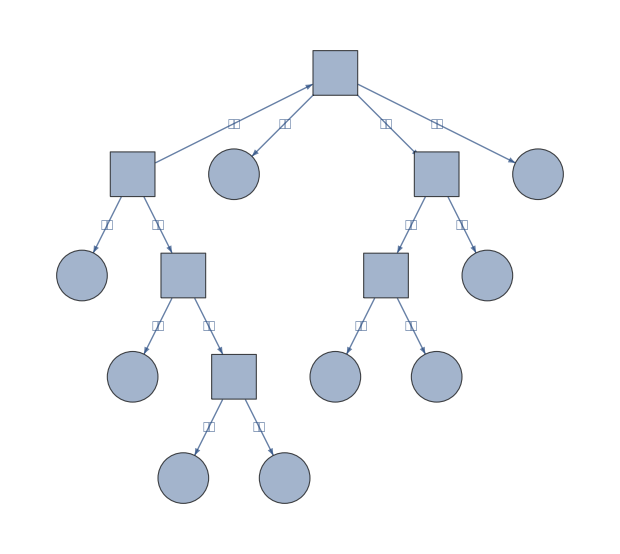

```mathematica
tree=TreeGenerate[trainingset,properties,SelectProperty->SelectGiniIndex];
DecisionTreeGraph[tree,properties]
```

```mathematica
BatchTestTree[tree,trainingset]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
_?(1&)//FullForm
```

PatternTest[Blank[],Function[1]]